## Setup

```mathematica
ScrollingOptions->{"VerticalScrollRange"->FitAll}
```

ScrollingOptions→{VerticalScrollRange→FitAll}

```mathematica
x1 = 0;
x2 = 1;
Clear[m,b]
m = 2/(x2 - x1)
Solve[m x1 + b == -1,b];
b = b/.%[[1]]
Num =240;(* 240 for gaussianR, 60 for linear*)
T[n_,u_]:=ChebyshevT[n,m u + b]
dT[n_,u_]:=m*Derivative[0,1][ChebyshevT][n,m u+b]
d2T[n_,u_]:=m^2* Derivative[0,2][ChebyshevT][n,m u+b]
c[j_]:= Piecewise[{{2,Abs[j]==Num},{2,j==0},{1,Abs[j]<Num}}]
p[j_]:= Piecewise[{{2,j==0},{2,j==Num},{1,0<j<Num}}]
Gridlist = ConstantArray[0,{Num+1}];
Gridlist =N [1/m(Cos[π#/Num]-b)&/@Range[0,Num],15]
Card[j_,u_]:= If[u==Gridlist[[j+1]],1,(-1)^(j+1)(1-(m u + b)^2)/(c[j] Num^2((m u+b)-(m Gridlist[[j+1]]+b)))1/m dT[Num,u]]
dCardM  =
 ConstantArray[0,{Num+1,Num+1}];
Module[
{i,j},
For[i=1,i≤Num+1,i++,For[j=1,j≤Num+1 ,j++,dCardM[[i,j]]=(-1)^(i+j)(m)p[i-1]/(p[j-1](m Gridlist[[i]]-m Gridlist[[j]]))]];
For[i=2,i≤Num,i++, dCardM[[i,i]]=-(m)(m*Gridlist[[i]]+b)/(2(1-(m*Gridlist[[i]]+b)^2))];
]
dCardM[[1,1]] =(m) (1+2 Num^2)/6;
dCardM[[Num+1,Num+1]] = -dCardM[[1,1]];
d2CardM = dCardM.dCardM;
```

2

-1

SetDelayed::write: Tag Real in 0.277997[n_, u_] is Protected.

$Failed

{1.,0.999957163787004,0.999828662487779,0.999614518120361,0.999314767377287,0.998929461619302,0.998458666866564,0.997902463787331,0.997260947684137,0.996534228477463,0.995722430686905,0.994825693409835,0.993844170297569,0.992778029529039,0.991627453781977,0.990392640201615,0.989073800366903,0.987671160254256,0.986184960198838,0.984615454853377,0.982962913144534,0.981227618226824,0.979409867434097,0.977509972228593,0.975528258147577,0.973465064747553,0.971320745546089,0.969095667961242,0.966790213248601,0.964404776435962,0.961939766255643,0.959395605074449,0.9567727288213,0.954071586912541,0.95129264217493,0.948436370766344,0.945503262094184,0.942493818731521,0.939408556330983,0.936248003536399,0.933012701892219,0.929703205750726,0.926320082177046,0.922863910851987,0.919335283972712,0.915734806151273,0.912063094311008,0.908320777580839,0.904508497187474,0.90062690634553,0.896676670145618,0.892658465440372,0.888572980728485,0.88442091603673,0.880202982800015,0.875919903739489,0.871572412738697,0.867161254717843,0.862687185506144,0.858150971712327,0.853553390593274,0.84889522992084,0.844177287846877,0.839400372766471,0.834565303179429,0.829672907550034,0.824724024165092,0.819719500990292,0.814660195524919,0.809546974654917,0.80438071450436,0.79916230028533,0.793892626146237,0.788572595018617,0.783203118462416,0.777785116509801,0.772319517507514,0.766807257957806,0.761249282357974,0.755646543038526,0.75,0.744310620748477,0.738579380129804,0.732807260162556,0.726995249869773,0.721144345109501,0.715255548404148,0.709329868768714,0.7033683215379,0.697371928192134,0.691341716182545,0.685278718754918,0.67918397477265,0.673058528538746,0.666903429616885,0.660719732651581,0.654508497187474,0.648270787487785,0.642007672351961,0.635720224932537,0.62940952255126,0.623076646514497,0.616722681927953,0.610348717510751,0.60395584540888,0.597545161008064,0.591117762746074,0.584674751924512,0.578217232520115,0.57174631099559,0.565263096110026,0.558768698728919,0.552264231633827,0.545750809331701,0.539229547863922,0.532701564615072,0.526167978121472,0.519629907879534,0.513088474153937,0.506544797785672,0.5,0.493455202214328,0.486911525846063,0.480370092120466,0.473832021878528,0.467298435384928,0.460770452136078,0.454249190668299,0.447735768366173,0.441231301271081,0.434736903889974,0.42825368900441,0.421782767479885,0.415325248075488,0.408882237253926,0.402454838991936,0.39604415459112,0.389651282489249,0.383277318072047,0.376923353485503,0.37059047744874,0.364279775067463,0.357992327648039,0.351729212512215,0.345491502812526,0.339280267348419,0.333096570383115,0.326941471461254,0.32081602522735,0.314721281245082,0.308658283817455,0.302628071807866,0.2966316784621,0.290670131231286,0.284744451595852,0.278855654890499,0.273004750130227,0.267192739837444,0.261420619870196,0.255689379251523,0.25,0.244353456961474,0.238750717642026,0.233192742042194,0.227680482492486,0.222214883490199,0.216796881537584,0.211427404981383,0.206107373853763,0.20083769971467,0.19561928549564,0.190453025345083,0.185339804475081,0.180280499009708,0.175275975834908,0.170327092449966,0.165434696820571,0.160599627233529,0.155822712153123,0.15110477007916,0.146446609406726,0.141849028287673,0.137312814493856,0.132838745282157,0.128427587261303,0.124080096260511,0.119797017199985,0.11557908396327,0.111427019271515,0.107341534559628,0.103323329854382,0.0993730936544697,0.0954915028125263,0.0916792224191605,0.0879369056889922,0.0842651938487274,0.080664716027288,0.0771360891480134,0.0736799178229539,0.0702967942492737,0.0669872981077807,0.0637519964636014,0.0605914436690173,0.0575061812684791,0.0544967379058161,0.0515636292336558,0.0487073578250697,0.0459284130874594,0.0432272711786996,0.0406043949255509,0.0380602337443566,0.0355952235640379,0.0332097867513991,0.0309043320387579,0.0286792544539108,0.0265349352524472,0.0244717418524232,0.0224900277714067,0.0205901325659035,0.0187723817731764,0.0170370868554659,0.0153845451466228,0.0138150398011617,0.0123288397457437,0.0109261996330972,0.00960735979838478,0.00837254621802271,0.00722197047096114,0.00615582970243114,0.00517430659016489,0.00427756931309479,0.00346577152253685,0.00273905231586333,0.00209753621266914,0.00154133313343601,0.00107053838069825,0.000685232622713063,0.000385481879638533,0.00017133751222136,0.0000428362129964839,0}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/(2 SuperscriptBox[x, 2]) + 1/x*radiallamblist[["<>ToString[i+1]<>"]]+1/2(radiallamblist[["<>ToString[i+1]<>"]])^2+ x*"<>"sigmadotsubscale"<>ToString[i]<>"[x]"]
,{i,0,15}];
```

## RN Longest Time

```mathematica
$PlotTheme = "Classic"
```

Classic

Defining a Deep Pulse

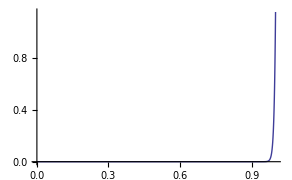
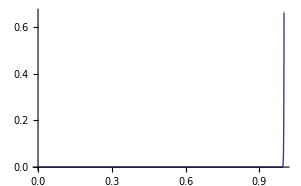
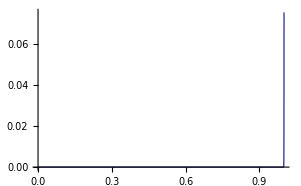

```mathematica
ListPlot[{pressureDeepSharp3RN80listϵ,pressureDeepSharp5RN80listϵ,pressureDeepSharp6RN80listϵ[[100;;]],pressureDeepSharp4RN80listϵ},PlotRange->All,AxesLabel->{"v ε^(1/4)","Anistropy"},AxesStyle->Large]
```

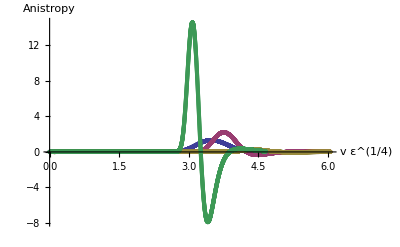

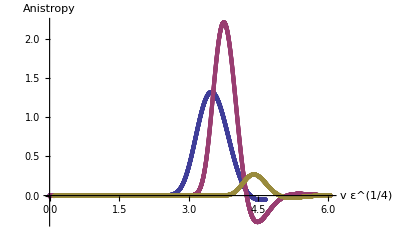

## Trying to find a Longest Time, using above “deepest pulse”, (r_ave = -2, A = 30).

Anyway,  If we just assume that this pulse is a good “deepest pulse” candidtate (r_ave = -2, A = 30), and we check out random values of epsilon and temparture we find:

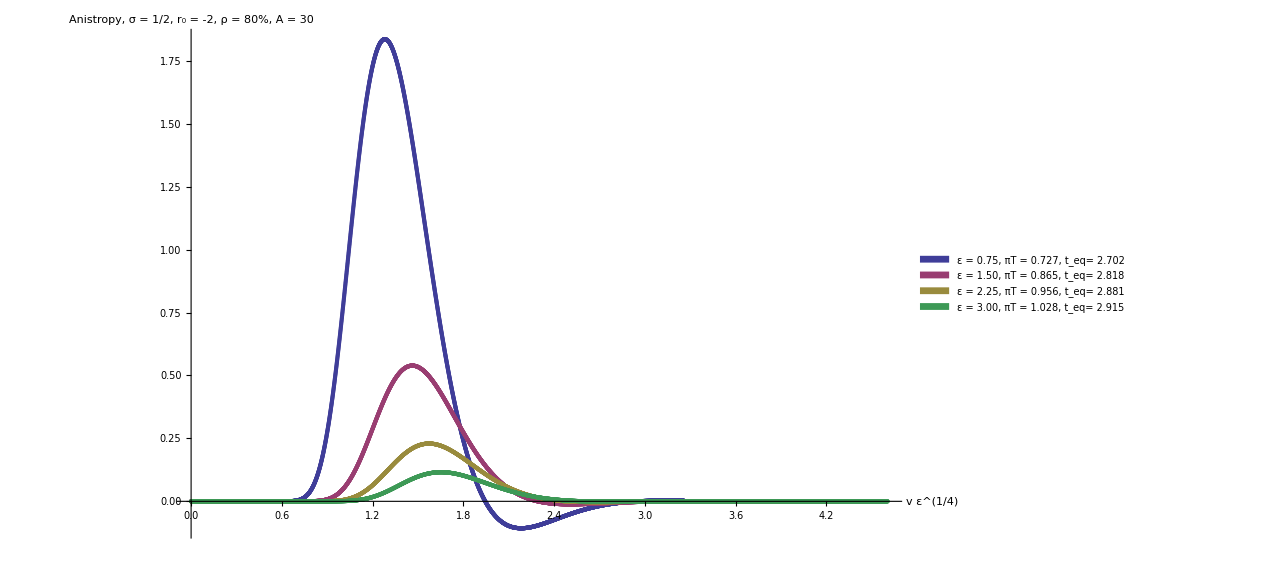

Now, the vartion of t_eq, COULD potentially be due to entering the linearized region, since the anisotropy is smaller than one for the other curves (although using boundary anisotropy as a measure of when you are and aren’t in the linear regime has shown to be a bad idea), but just to be sure, I will rerun the curves, and this time I’ll keep A/ε constant.

We find:

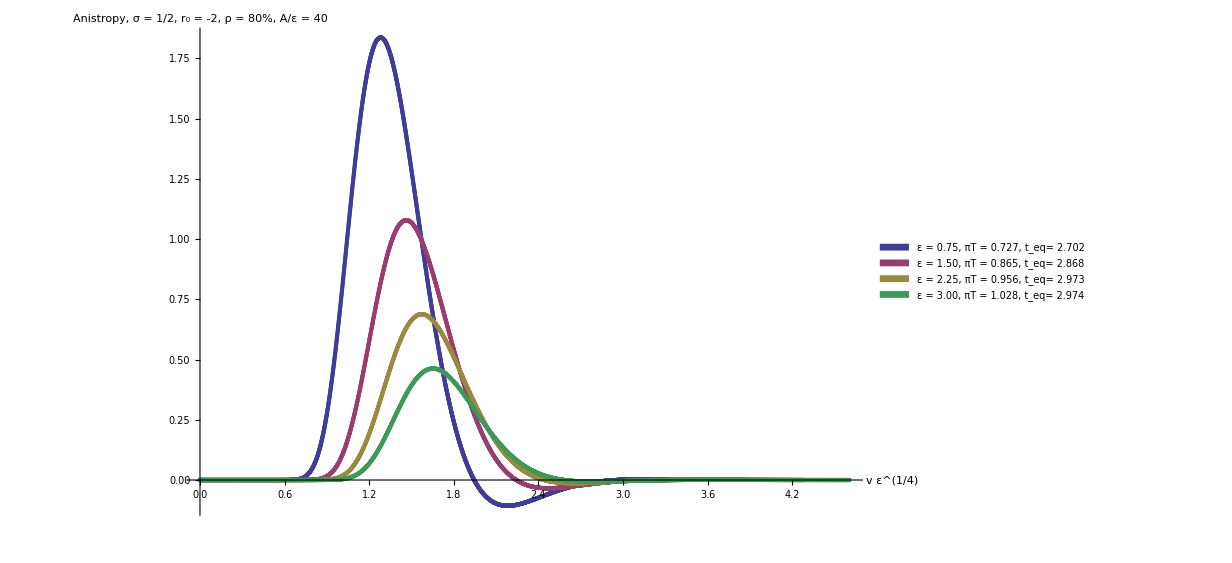

Wow.  That didn’t help the situation.  t_eq variation got worse.

Finally, for the sake of completness, lets check in units of temperature, t_eq is now given in units of π T

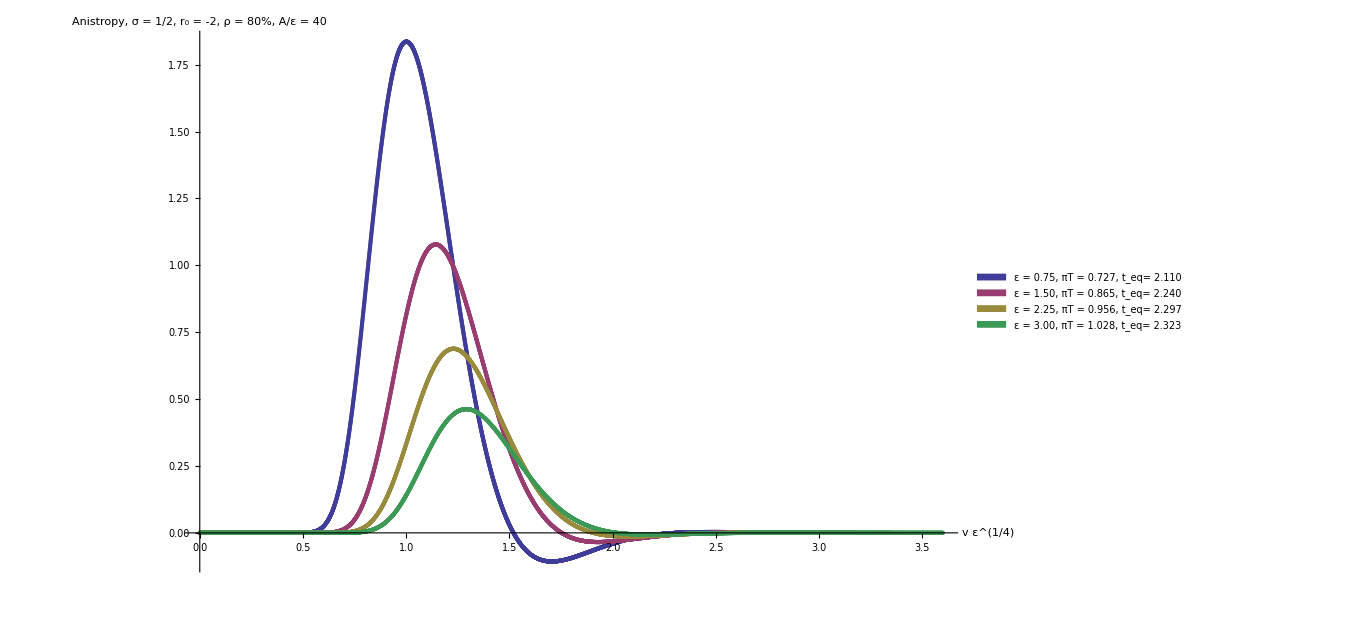

Larry,  All times are roughly constant, well within the variation what had from just defining a good “deep pulse”.

This is muddied but in that,  by changing epsilon, the horizon moves, essentially making the initial B_sub look slightly different (in a similar way that moving r_ave, and A does), and thus varies t_eq, as we saw at the very top!

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.43319×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.67398×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

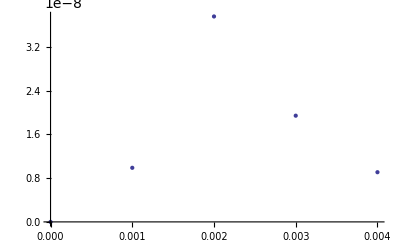

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

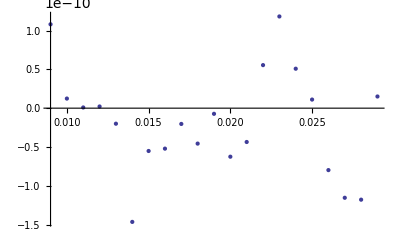

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

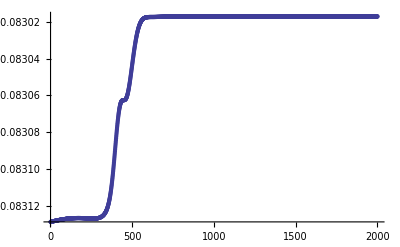

```mathematica
ListPlot[lamblist,PlotRange->All]
```

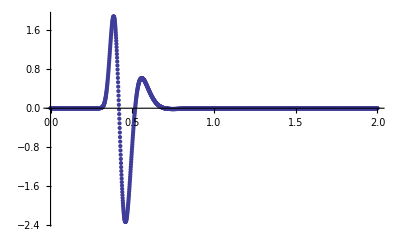

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

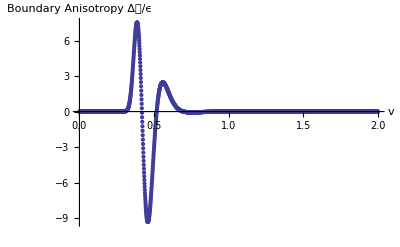

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
pressureRN80listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
3/(4π T)
```

1.03162

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.1242×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 **, rave = 1/4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.77316×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.10701×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.27329×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99389×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

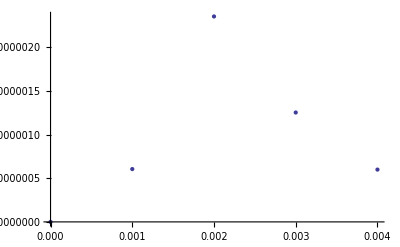

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

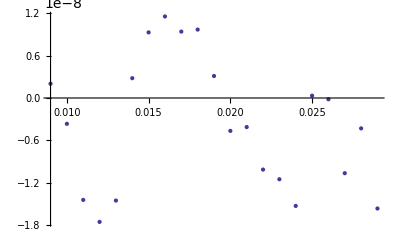

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

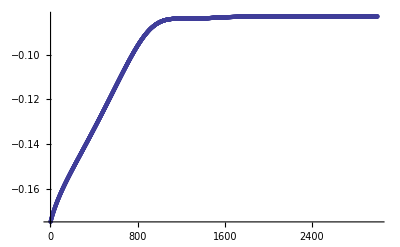

```mathematica
ListPlot[lamblist,PlotRange->All]
```

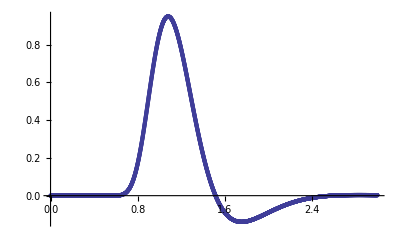

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

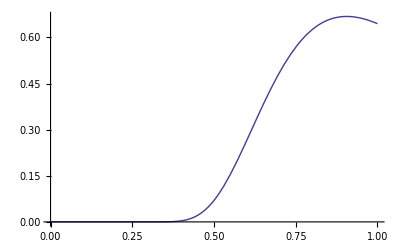

```mathematica
Plot[Bsub1[x],{x,0,1}]
```

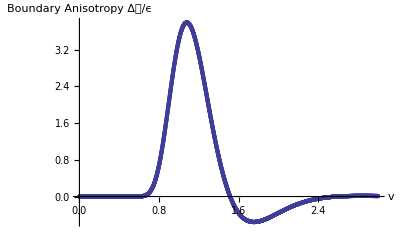

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeep2RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeep2RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231414

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.07329×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/20

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.77316×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.53164×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.36646×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98829×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

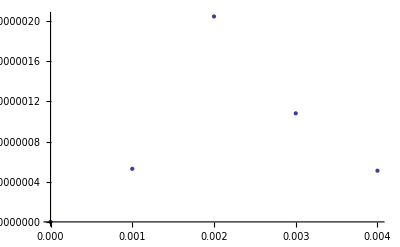

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

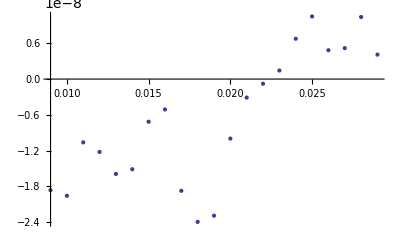

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

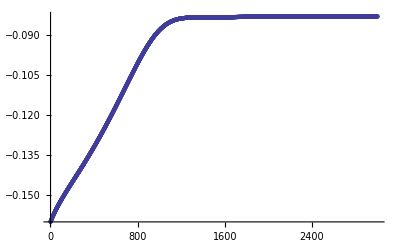

```mathematica
ListPlot[lamblist,PlotRange->All]
```

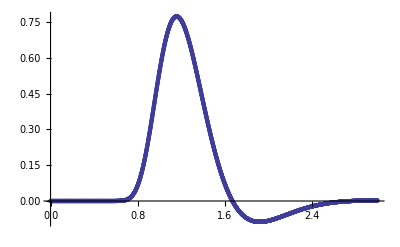

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

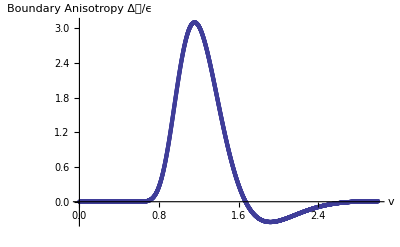

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeeperRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeeperRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.88156×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/100

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.6396×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99478×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

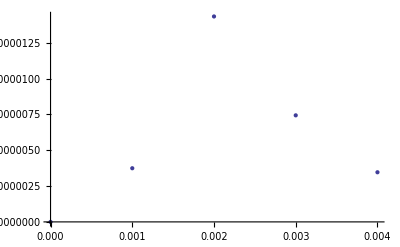

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

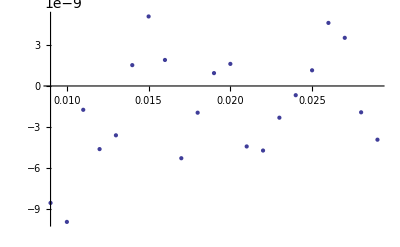

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

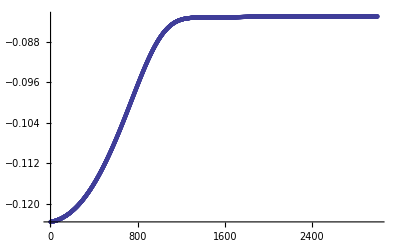

```mathematica
ListPlot[lamblist,PlotRange->All]
```

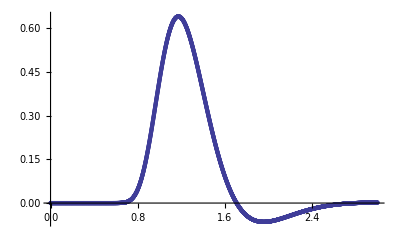

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

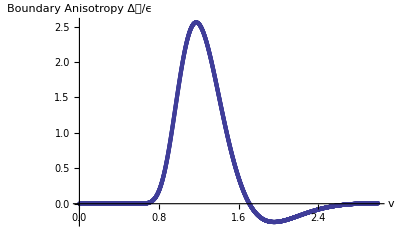

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepestRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepestRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.45523×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.88658×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.23706×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.88851×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.18323×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99728×10^-12

### Plots

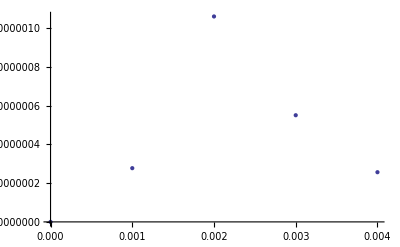

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

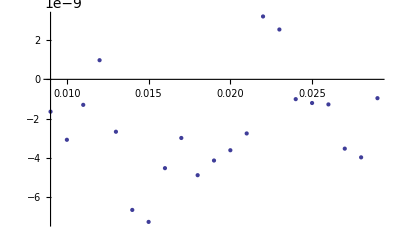

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

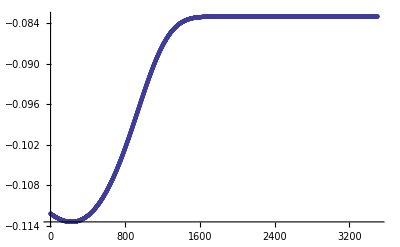

```mathematica
ListPlot[lamblist,PlotRange->All]
```

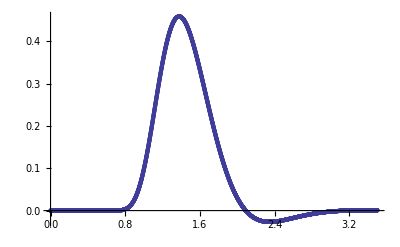

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

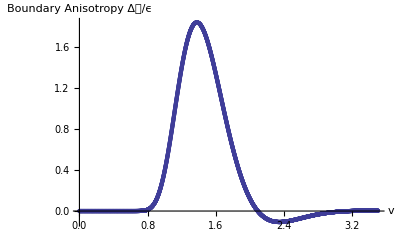

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepN2RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepN2RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.74969×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4 width = 0.25

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp25wid0.25uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp25wid0.25uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.77316×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.9476×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.36721×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.18323×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99828×10^-12

### Plots

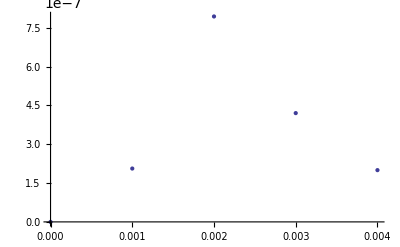

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

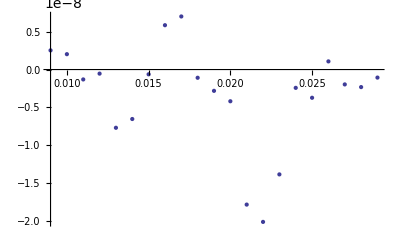

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

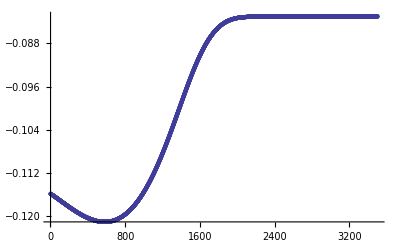

```mathematica
ListPlot[lamblist,PlotRange->All]
```

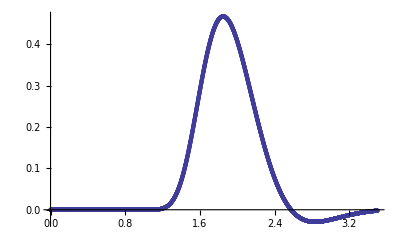

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

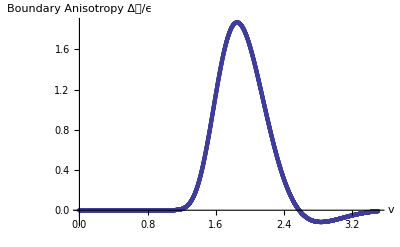

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.7022×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4 width = 0.125

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp900000wid0.125uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp900000wid0.125uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.88738×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.35558×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99578×10^-12

### Plots

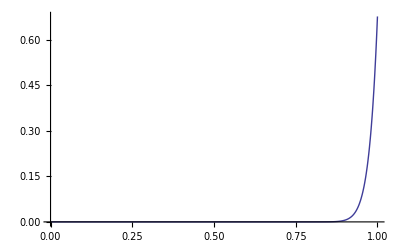

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

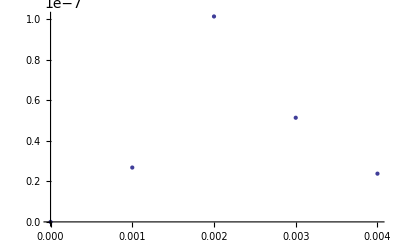

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

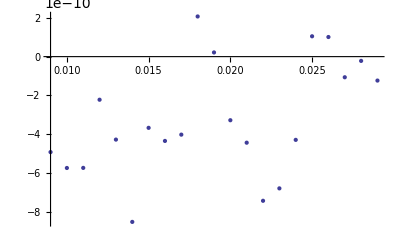

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

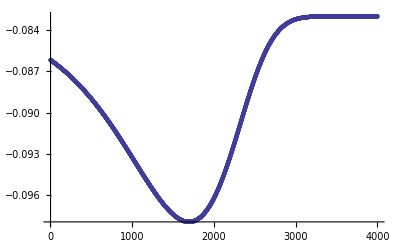

```mathematica
ListPlot[lamblist,PlotRange->All]
```

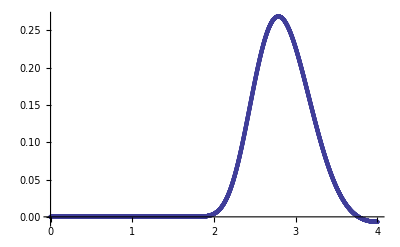

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

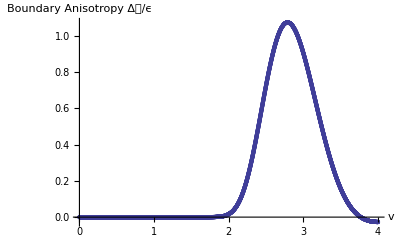

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharp2RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharp2RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231414

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.33077×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189438

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4 width = 0.0625

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp4.3e+24wid0.0625uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp4.3e+24wid0.0625uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.10862×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.23706×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.23186×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99462×10^-12

### Plots

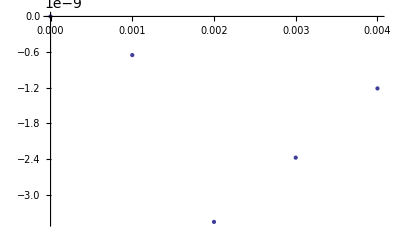

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

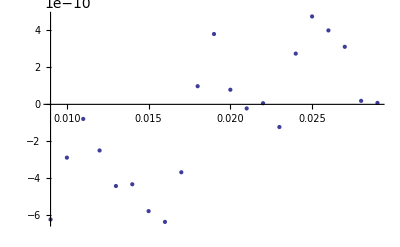

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

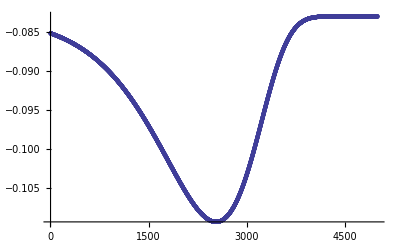

```mathematica
ListPlot[lamblist,PlotRange->All]
```

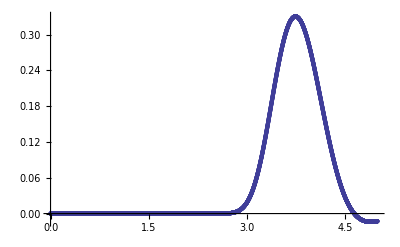

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

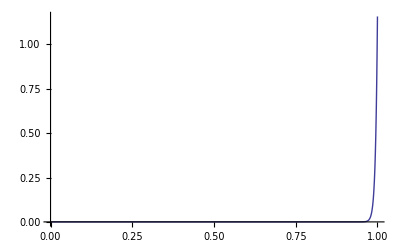

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

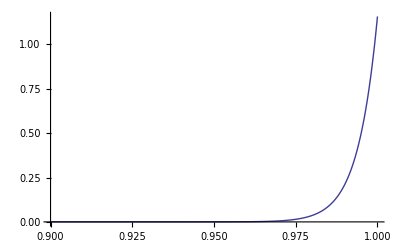

```mathematica
Plot[Bsub1[x],{x,0.9,1},PlotRange->All]
```

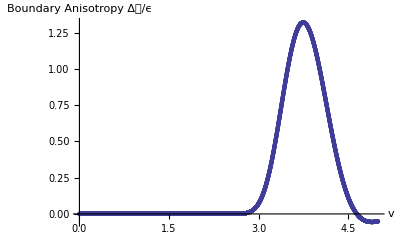

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharp3RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharp3RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231414

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.79092×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189438

## Obn Pulse NL

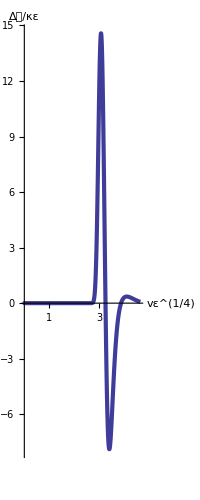

```mathematica
ListPlot[{pressureDeepSharp4RN80listϵ},Joined->True,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},AxesStyle->Directive[26,Black],AspectRatio->Full,ImageSize->{{300},{200}},Ticks->{{1,2,3,4},Automatic}]
```

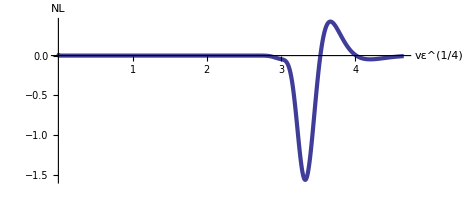

```mathematica
ListPlot[Table[{pressureDeepSharp4RN80listϵ[[i,1]],pressureDeepSharp4RN80listϵ[[i,2]]-2*pressureDeepSharp4RN80halfamplistϵ[[i,2]]},{i,1,Length[pressureDeepSharp4RN80listϵ]}],Joined->True,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{1,2,3,4},Automatic},ImageSize->{{300},{200}},AspectRatio->Full]
```

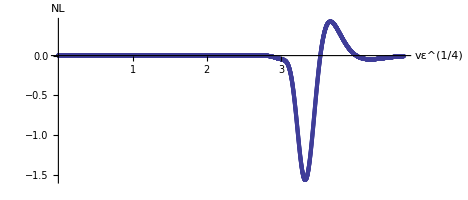

```mathematica
ListPlot[Table[{pressureDeepSharp4RN80listϵ[[i,1]],pressureDeepSharp4RN80listϵ[[i,2]]-2*pressureDeepSharp4RN80halfamplistϵ[[i,2]]},{i,1,Length[pressureDeepSharp4RN80listϵ]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{1,2,3},Automatic},ImageSize->{{300},{200}},AspectRatio->Full]
```

```mathematica
1.5/15
```

0.1

```mathematica
𝒫𝒸
```

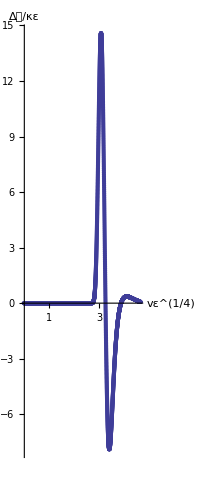

```mathematica
ListPlot[{pressureDeepSharp4RN80listϵ},PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{1,2,3},Automatic},ImageSize->{{300},{200}},AspectRatio->Full]
```

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1 width = 0.005 (obn. pulse)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.9wid0.005uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.9wid0.005uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.15463×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.41585×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.14768×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Plots

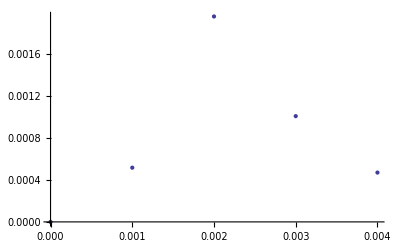

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

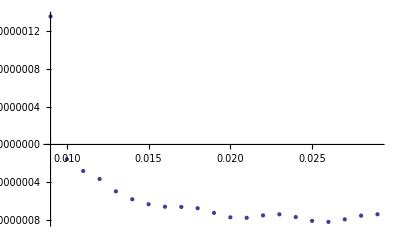

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

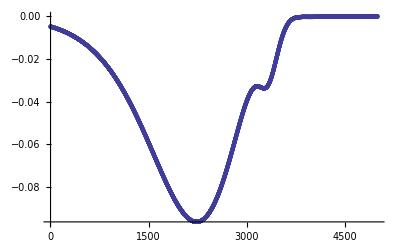

```mathematica
ListPlot[lamblist,PlotRange->All]
```

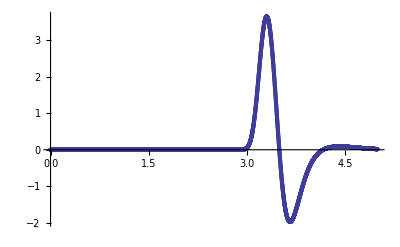

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

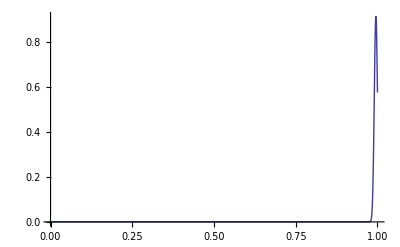

```mathematica
Plot[{Bsub1[x]},{x,0,1},PlotRange->All]
```

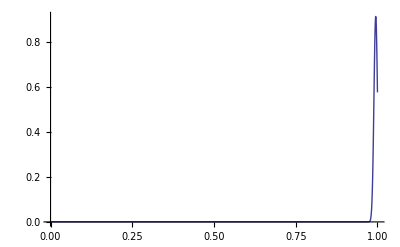

```mathematica
Plot[{Bsub2[x]},{x,0,1},PlotRange->All]
```

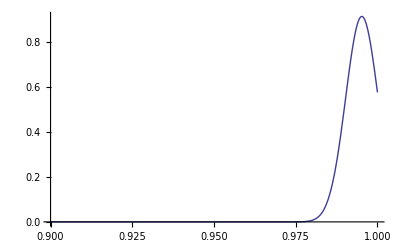

```mathematica
Plot[Bsub1[x],{x,0.9,1},PlotRange->All]
```

```mathematica
ultrafinegrid = Table[i*1/100000,{i,0,100000}];
```

```mathematica
temptemplist = Bsub1[ultrafinegrid];
```

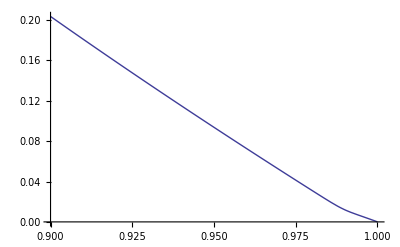

```mathematica
Plot[sigmadot1[x],{x,0.9,1}]
```

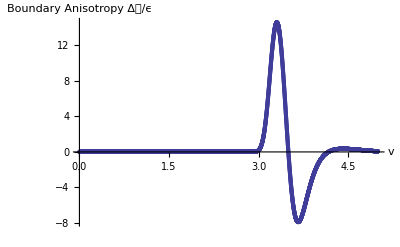

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharp4RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharp4RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

```mathematica
ListPlot[{pressureDeep2RN0listϵ,pressureDeep2RN20listϵ,pressureDeep2RN40listϵ,pressureDeep2RN60listϵ,pressureDeep2RN80listϵ},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["20%",22],Style["40%",22], Style["60%",22], Style["80%",22]}],{.76,.68}],AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},ImageSize->{{400},{300}},AspectRatio->Full]
```

```mathematica
ListPlot[{pressureDeepSharp4RN80listϵ},Joined->True,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},AxesStyle->Directive[26,Black],AspectRatio->Full,ImageSize->{{300},{200}},Ticks->{{1,2,3},Automatic}]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.001];
```

```mathematica
reportfuncttlist
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95}

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve, 
AxesLabel->{"vε^(1/4)     ",Style["   u",30,Italic, FontFamily->"Times",Black], Style["B_s    ",30,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[26,Black],PlotRange->All,ColorFunction->Function[{x,y,z},Hue[0.6z+0.45]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

```mathematica
ListPlot3D[Bsubevolve, 
AxesLabel->{"vε^(1/4)   ",Style["   u",28,Italic, FontFamily->"Times",Black], Style["B_s   ",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->All,ColorFunction->Function[{x,y,z},Hue[0.6z+0.45]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.315036

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.387108

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.688377

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.533137

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1 width = 0.005 (obn. pulse)(half amp)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.45wid0.005uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.45wid0.005uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS5000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.15463×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.41585×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.14768×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Plots

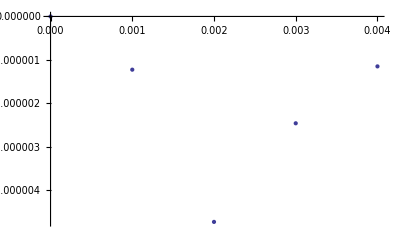

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

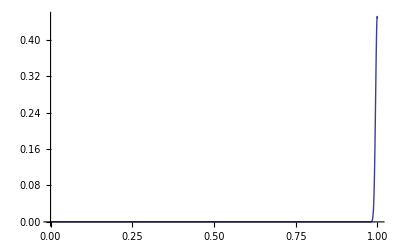

```mathematica
Plot[{Bsub1[x]},{x,0,1},PlotRange->All]
```

```mathematica
Plot[{Bsub2[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0.9,1},PlotRange->All]
```

-Graphics-

```mathematica
ultrafinegrid = Table[i*1/100000,{i,0,100000}];
```

```mathematica
temptemplist = Bsub1[ultrafinegrid];
```

```mathematica
Plot[sigmadot1[x],{x,0.9,1}]
```

-Graphics-

```mathematica
g=1
```

1

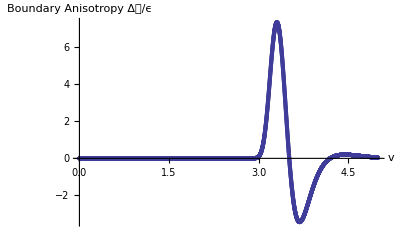

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharp4RN80halfamplist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharp4RN80halfamplistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

```mathematica
ListPlot[{pressureDeep2RN0listϵ,pressureDeep2RN20listϵ,pressureDeep2RN40listϵ,pressureDeep2RN60listϵ,pressureDeep2RN80listϵ},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["20%",22],Style["40%",22], Style["60%",22], Style["80%",22]}],{.76,.68}],AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},ImageSize->{{400},{300}},AspectRatio->Full]
```

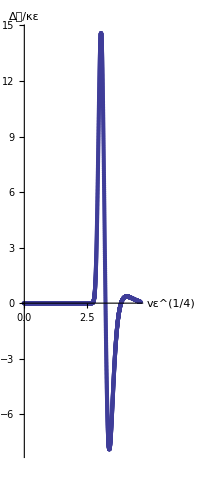

```mathematica
ListPlot[pressureDeepSharp4RN80listϵ,AxesStyle->Directive[22,Black],PlotRange->All,AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28]},ImageSize->{{400},{300}},AspectRatio->Full]
```

```mathematica
finegrid = Range[0,1,0.001];
```

```mathematica
reportfuncttlist
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95}

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
{Style["NL",26,Black]},AxesStyle->Directive[26,Black],AspectRatio->Full,ImageSize->{{300},{200}}, v 24, ε26}
```

```mathematica
ListPlot3D[Bsubevolve, 
AxesLabel->{"vε^(1/4)     ",Style["   u",30,Italic, FontFamily->"Times",Black], Style["B_s     ",30,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[26,Black],PlotRange->All,ColorFunction->Function[{x,y,z},Hue[0.6z+0.45]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.315036

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.387108

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.688377

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.533137

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4 width = 0.005

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.95e+21wid0.01uave1.11111111111a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS6500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.95e+21wid0.01uave1.11111111111a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS6500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.66533×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.61282×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Plots

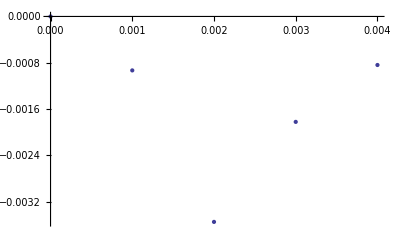

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

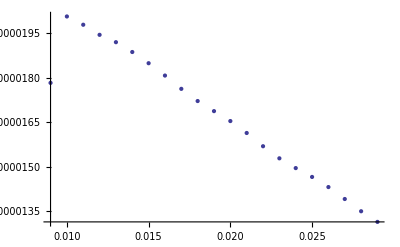

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

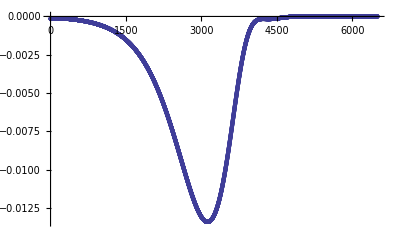

```mathematica
ListPlot[lamblist,PlotRange->All]
```

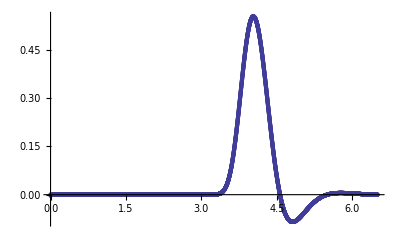

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

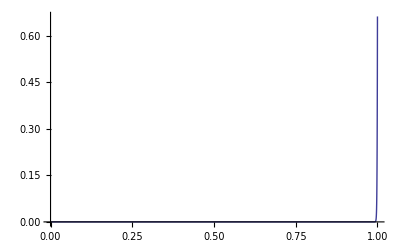

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

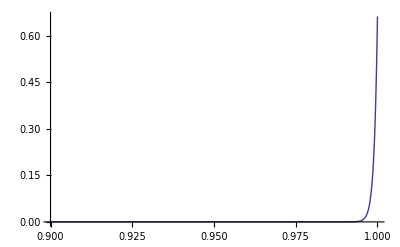

```mathematica
Plot[Bsub1[x],{x,0.9,1},PlotRange->All]
```

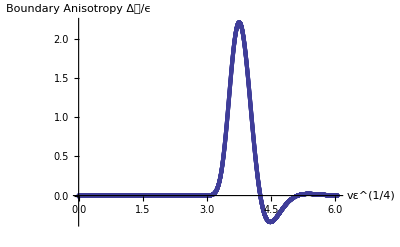

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharp5RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharp5RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["vε^(1/4)",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
reportfuncttlist
```

{0.,0.065,0.13,0.195,0.26,0.325,0.39,0.455,0.52,0.585,0.65,0.715,0.78,0.845,0.91,0.975,1.04,1.105,1.17,1.235,1.3,1.365,1.43,1.495,1.56,1.625,1.69,1.755,1.82,1.885,1.95,2.015,2.08,2.145,2.21,2.275,2.34,2.405,2.47,2.535,2.6,2.665,2.73,2.795,2.86,2.925,2.99,3.055,3.12,3.185,3.25,3.315,3.38,3.445,3.51,3.575,3.64,3.705,3.77,3.835,3.9,3.965,4.03,4.095,4.16,4.225,4.29,4.355,4.42,4.485,4.55,4.615,4.68,4.745,4.81,4.875,4.94,5.005,5.07,5.135,5.2,5.265,5.33,5.395,5.46,5.525,5.59,5.655,5.72,5.785,5.85,5.915,5.98,6.045,6.11,6.175,6.24,6.305,6.37,6.435}

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve, 
AxesLabel->{"vε^(1/4)",Style["u",28,Italic, FontFamily->"Times",Black], Style["B_s",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->All,ColorFunction->Function[{x,y,z},Hue[1.1z+0.1]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.68327×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 340 ** rave = 1/4 ULTRA SHARP

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN340amp5e+85wid0.005uave1.11111111111a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS6500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN340amp5e+85wid0.005uave1.11111111111a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS6500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.20417×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.69482×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.38556×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.29559×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.55271×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.998×10^-12

### Plots

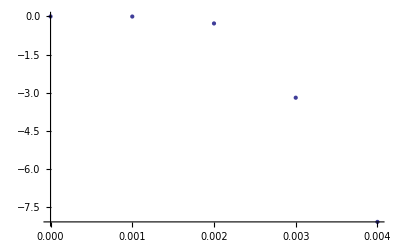

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

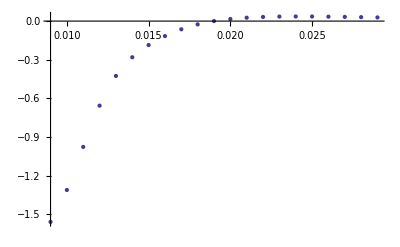

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

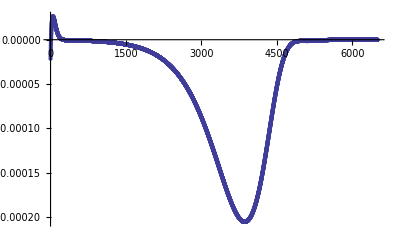

```mathematica
ListPlot[lamblist,PlotRange->All]
```

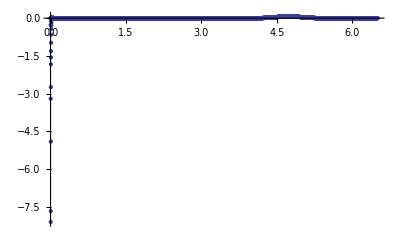

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

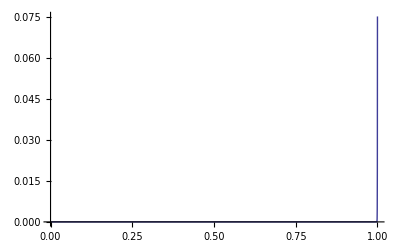

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

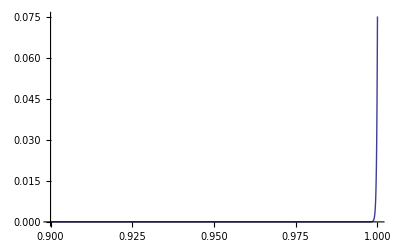

```mathematica
Plot[Bsub1[x],{x,.9,1},PlotRange->All]
```

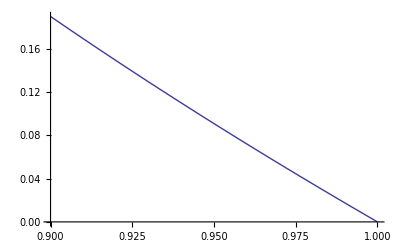

```mathematica
Plot[sigmadot1[x],{x,0.9,1}]
```

```mathematica
templist
```

{-2.49578×10^-13,-0.010652,-1.10016,-12.8012,-32.3716,-30.6675,-19.6119,-10.9408,-7.34217,-6.23525,«6481»,0.0016322,0.00163521,0.00163819,0.00164124,0.00164419,0.00164712,0.00165018,0.00165319,0.00165601,0.00165885}

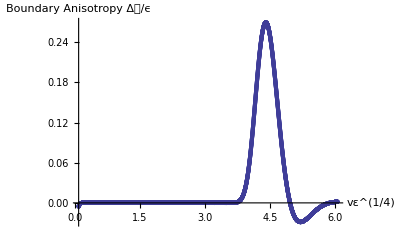

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharp6RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharp6RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,100,Length[tlist]}],PlotRange->All,AxesLabel->{Style["vε^(1/4)",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve, 
AxesLabel->{"      vε^(1/4)",Style["u",28,Italic, FontFamily->"Times",Black], Style["       B_s",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->All,ColorFunction->Function[{x,y,z},Hue[1.1z+0.1]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.315036

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.387108

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.688377

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.533137

Now, lets see if we try a bunch of random epsilons, at 80% extremality, and thus different temperatures, if they all seem to have a maximal time, in terms of epsilon.

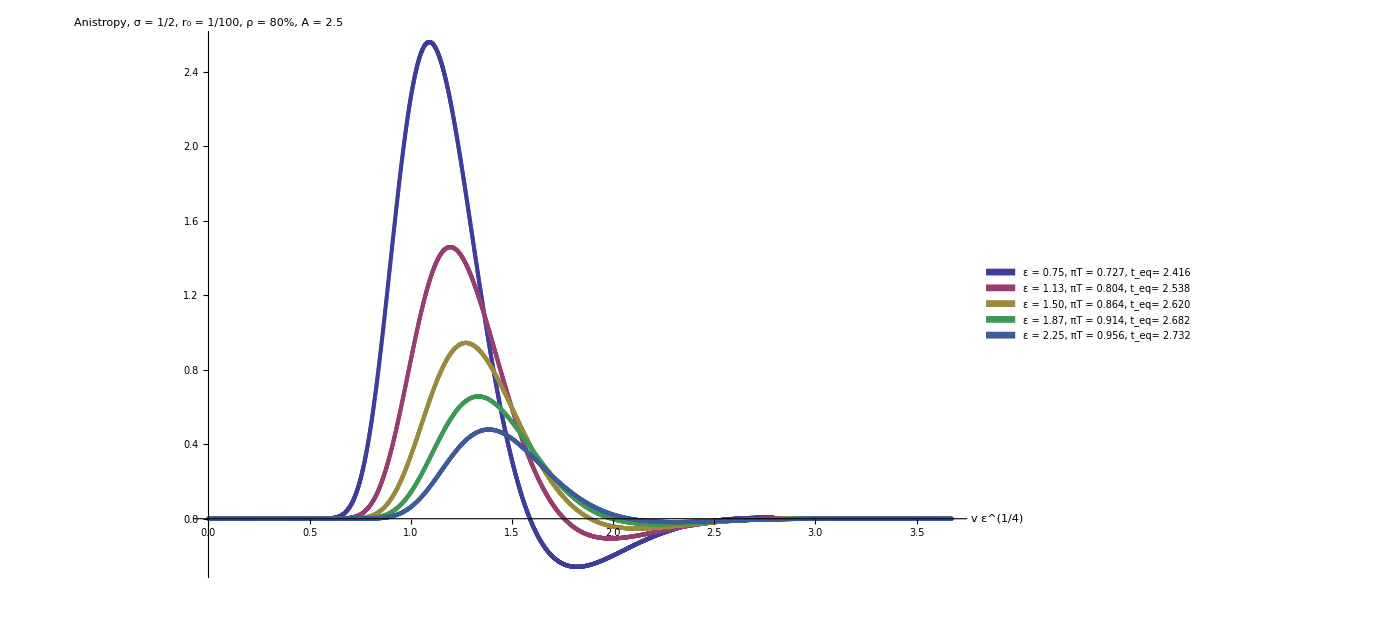

```mathematica
ListPlot[{pressureDeepestRN80listϵ,pressureRN80curve2listϵ,pressureRN80curve3listϵ,pressureRN80curve4listϵ,pressureRN80curve5listϵ},PlotRange->All, AxesLabel->{"v ε^(1/4)","Anistropy, σ = 1/2, r_0 = 1/100, ρ = 80%, A = 2.5"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["ε = 0.75, πT = 0.727, t_eq= 2.416",22],Style["ε = 1.13, πT = 0.804, t_eq= 2.538",22],Style["ε = 1.50, πT = 0.864, t_eq= 2.620",22],Style["ε = 1.87, πT = 0.914, t_eq= 2.682",22],Style["ε = 2.25, πT = 0.956, t_eq= 2.732",22]}],{Right,Top}]]
```

The times to reach 1% of isotropy are

```mathematica
3/4*4
```

3

```mathematica
2.68*4/3
```

3.57333

```mathematica
{t1,t2,t3,t4,t5,t6}
```

{2.41607,2.53809,2.6206,2.68269,2.73239,2.74632}

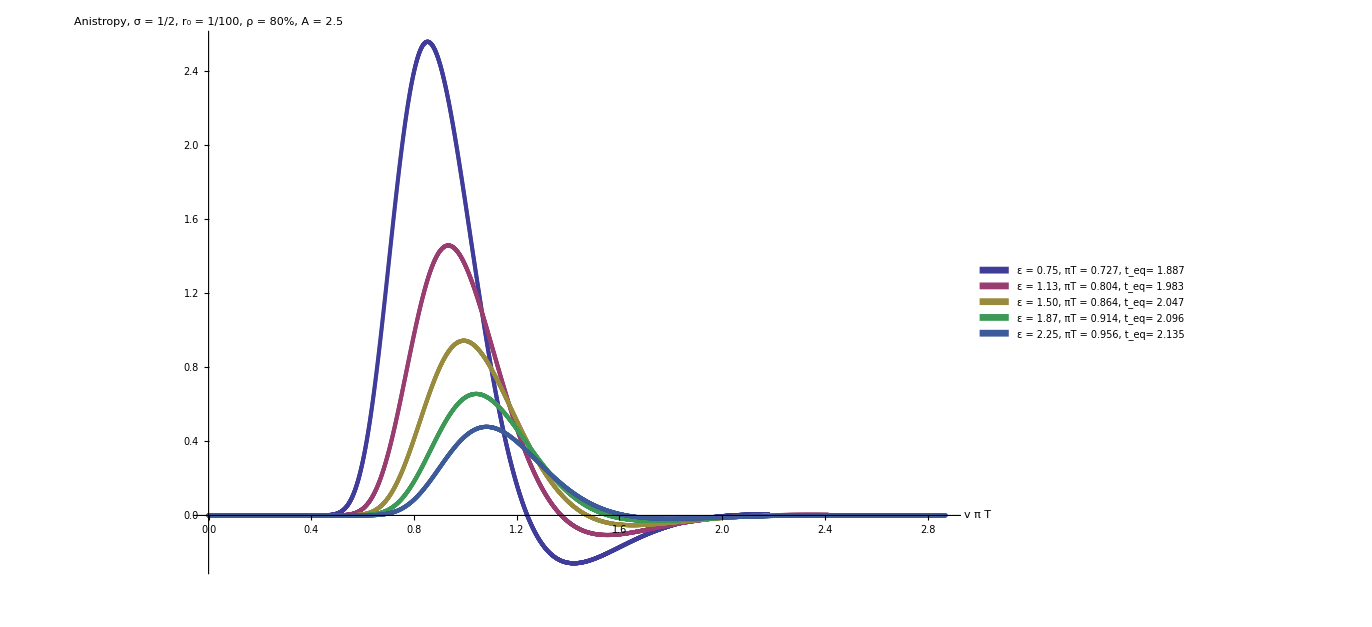

```mathematica
ListPlot[{pressureDeepestRN80listT,pressureRN80curve2listT,pressureRN80curve3listT,pressureRN80curve4listT,pressureRN80curve5listT},PlotRange->All,AxesLabel->{"v π T","Anistropy, σ = 1/2, r_0 = 1/100, ρ = 80%, A = 2.5"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["ε = 0.75, πT = 0.727, t_eq= 1.887",22],Style["ε = 1.13, πT = 0.804, t_eq= 1.983",22],Style["ε = 1.50, πT = 0.864, t_eq= 2.047",22],Style["ε = 1.87, πT = 0.914, t_eq= 2.096",22],Style["ε = 2.25, πT = 0.956, t_eq= 2.135",22]}],{Right,Top}]]
```

```mathematica
{tT1,tT2,tT3,tT4,tT5,tT6}
```

{1.88749,1.98281,2.04728,2.09578,2.13461,2.14549}

```mathematica
perc = 0.01
tempy = Interpolation[pressureRN80curve5listT]
tempmax = Max[Abs[Table[pressureRN80curve5listT[[i,2]],{i,1,Length[pressureRN80curve5listT]}]]]
```

0.01

InterpolatingFunction[{{0.,2.8704}},<>]

0.478732

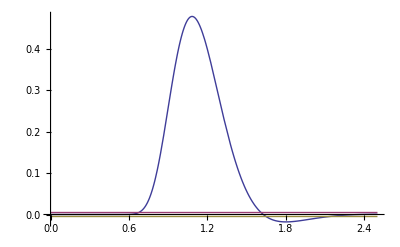
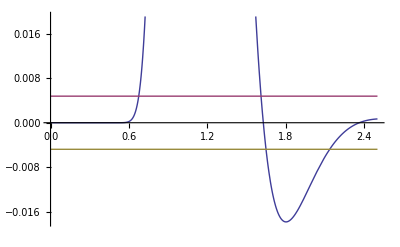

```mathematica
{Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,2.5},PlotRange->All],Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,2.5}]}
```

```mathematica
tT5 = FindRoot[tempy[x]+perc tempmax,{x,0,2.14}][[1,2]]
```

2.13461

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/100

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.6396×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99478×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepestRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepestRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
π T
```

0.72701

```mathematica
pressureDeepestRN80listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.45523×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/100

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-1.5f31.1651802521fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-1.5f31.1651802521fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.22125×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.55795×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.06581×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.63408×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96481×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

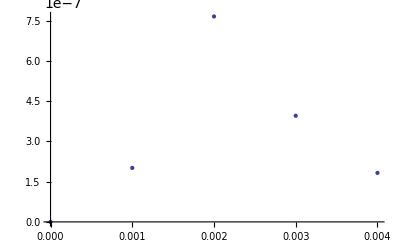

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

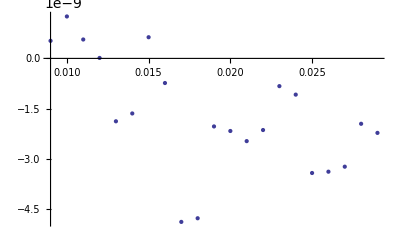

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

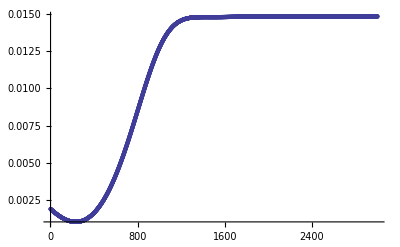

```mathematica
ListPlot[lamblist,PlotRange->All]
```

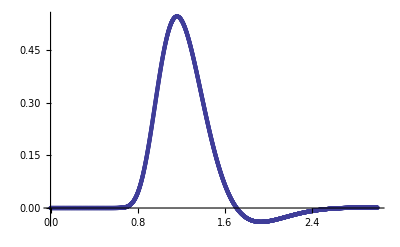

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

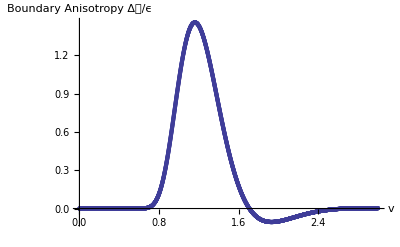

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80curve2list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80curve2listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256102

```mathematica
π T
```

0.804569

```mathematica
pressureRN80curve2listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.565711

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.125

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.88864×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.28324

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.284156

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/100

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.10623×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.80029×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.02318×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99589×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

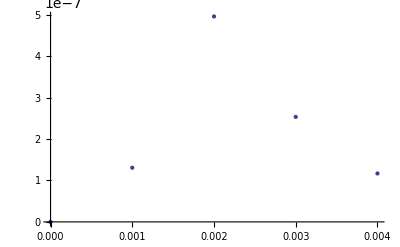

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

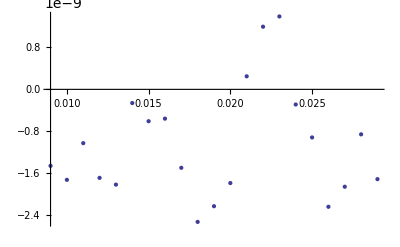

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

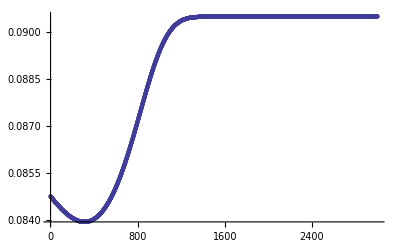

```mathematica
ListPlot[lamblist,PlotRange->All]
```

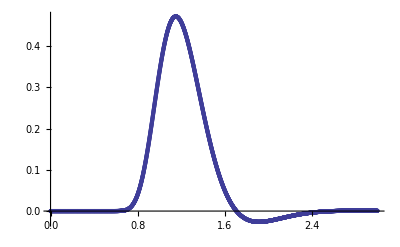

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

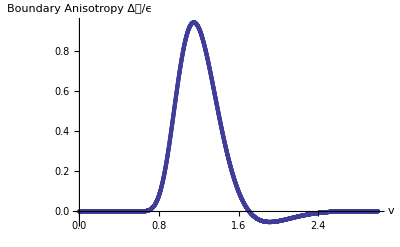

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80curve3list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80curve3listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.2752

```mathematica
π T
```

0.864566

```mathematica
pressureRN80curve3listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.607896

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.07684×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.07386

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.378874

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/100

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-2.5f31.70914802558fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-2.5f31.70914802558fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.60822×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.12639×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.5153×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97091×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

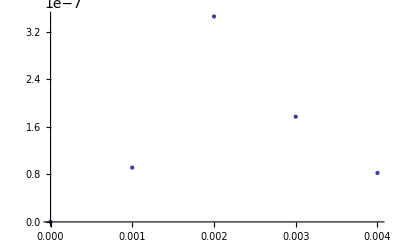

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

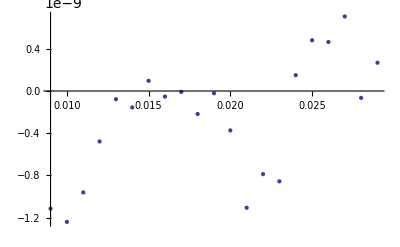

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

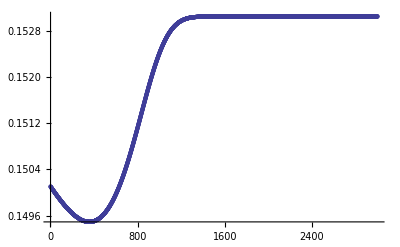

```mathematica
ListPlot[lamblist,PlotRange->All]
```

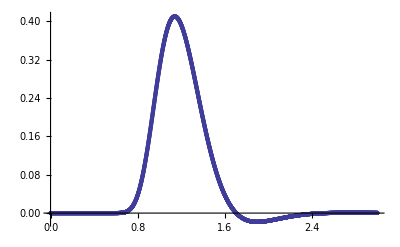

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

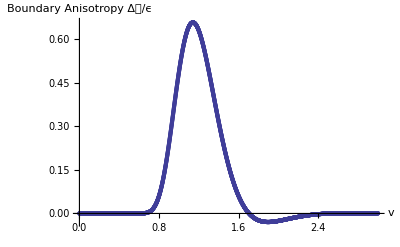

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80curve4list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80curve4listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.290988

```mathematica
π T
```

0.914167

```mathematica
pressureRN80curve4listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.642772

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.875

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.33894×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.81603

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.473593

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/100

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.5wid0.5uave100.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.77556×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.61853×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.27351×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94449×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

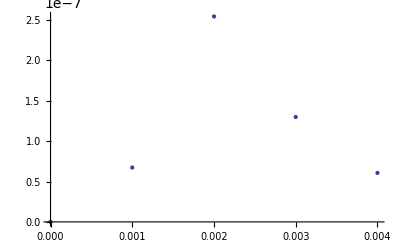

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

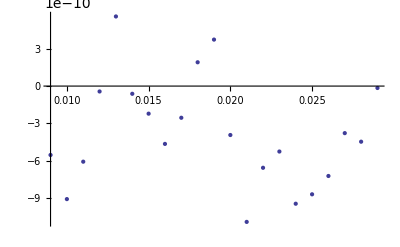

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

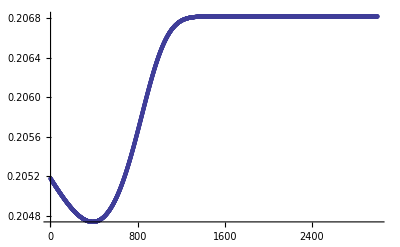

```mathematica
ListPlot[lamblist,PlotRange->All]
```

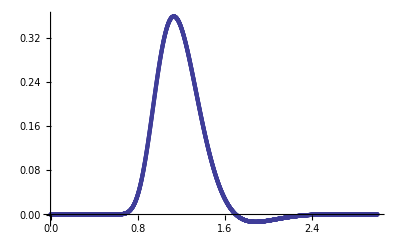

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

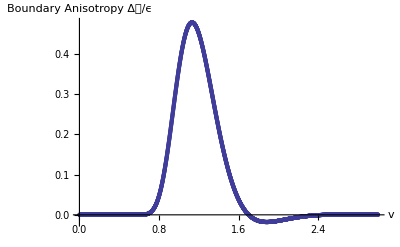

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80curve5list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80curve5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.304559

```mathematica
π T
```

0.956799

```mathematica
pressureRN80curve5listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.672748

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

2.25

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.78547×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.52172

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.568311

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/100

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp4.5wid0.5uave100.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp4.5wid0.5uave100.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.28484×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98224×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

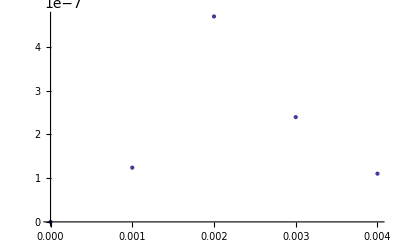

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

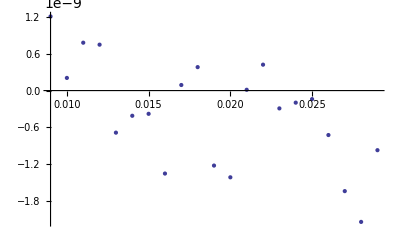

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

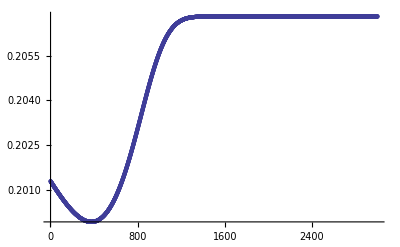

```mathematica
ListPlot[lamblist,PlotRange->All]
```

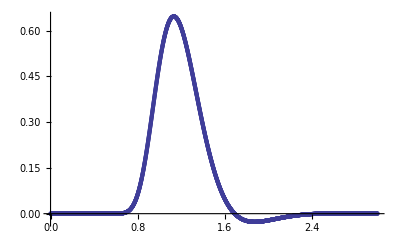

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

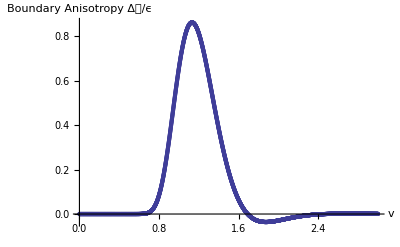

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80curve6list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80curve6listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.304559

```mathematica
pressureRN80curve6listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.672748

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

2.25

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.63196×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.52172

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.568311

AGAIN rave = -2

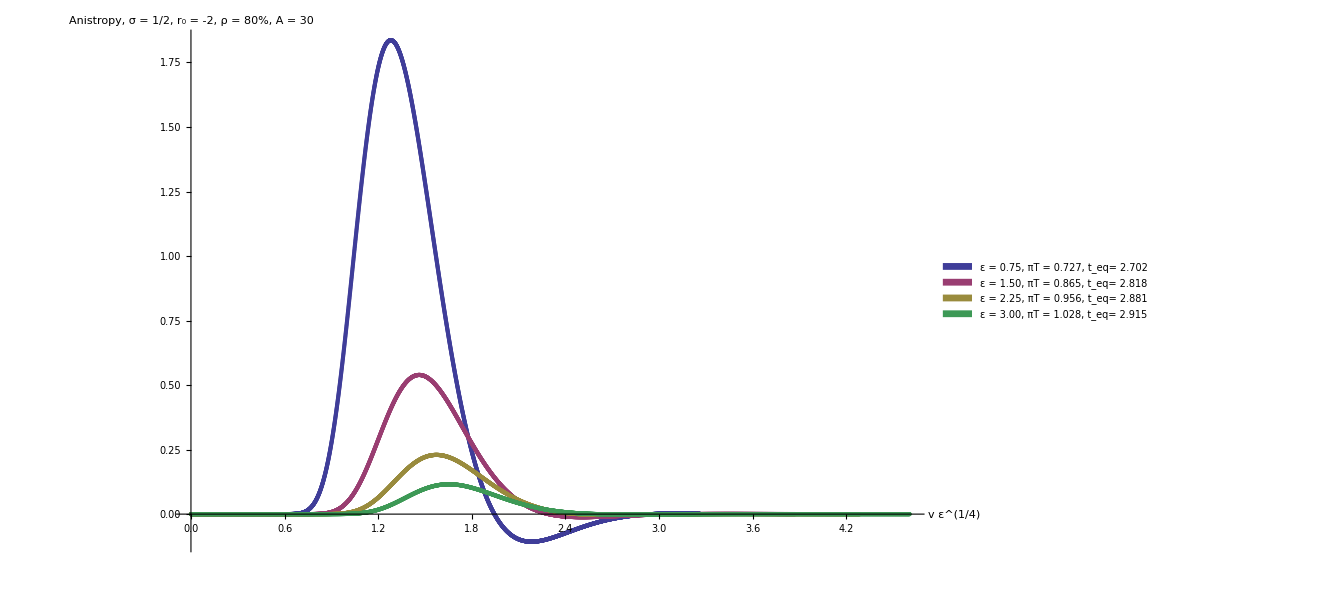

```mathematica
ListPlot[{pressureDeepN2RN80listϵ,pressureN2RN80curve2listϵ,pressureN2RN80curve3listϵ,pressureN2RN80curve4listϵ},PlotRange->All, AxesLabel->{"v ε^(1/4)","Anistropy, σ = 1/2, r_0 = -2, ρ = 80%, A = 30"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["ε = 0.75, πT = 0.727, t_eq= 2.702",22],Style["ε = 1.50, πT = 0.865, t_eq= 2.818",22],Style["ε = 2.25, πT = 0.956, t_eq= 2.881",22],Style["ε = 3.00, πT = 1.028, t_eq= 2.915",22]}],{Right,Top}]]
```

```mathematica
{2.70152,2.8177,2.88160,2.91520}
```

```mathematica
ListPlot[{pressureDeepN2RN80listϵ,pressureN2RN80AMPcurve2listϵ,pressureN2RN80AMPcurve3listϵ,pressureN2RN80AMPcurve4listϵ},PlotRange->All, AxesLabel->{"v ε^(1/4)","Anistropy, σ = 1/2, r_0 = -2, ρ = 80%, A/ε = 40"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["ε = 0.75, πT = 0.727, t_eq= 2.702",22],Style["ε = 1.50, πT = 0.865, t_eq= 2.868",22],Style["ε = 2.25, πT = 0.956, t_eq= 2.973",22],Style["ε = 3.00, πT = 1.028, t_eq= 2.974",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
{2.70152,2.868,2.9396540484434204,2.9738270288068587}
```

```mathematica
ListPlot[{pressureDeepN2RN80listT,pressureN2RN80AMPcurve2listT,pressureN2RN80AMPcurve3listT,pressureN2RN80AMPcurve4listT},PlotRange->All, AxesLabel->{"v π T","Anistropy, σ = 1/2, r_0 = -2, ρ = 80%, A/ε = 40"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["ε = 0.75, πT = 0.727, t_eq= 2.110",22],Style["ε = 1.50, πT = 0.865, t_eq= 2.240",22],Style["ε = 2.25, πT = 0.956, t_eq= 2.297",22],Style["ε = 3.00, πT = 1.028, t_eq= 2.323",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
ListPlot[pressureN2RN80AMPcurve4listϵ]
```

-Graphics-

```mathematica
{2.110,2.240,2.296,2.323}
```

{2.11,2.24,2.296,2.323}

```mathematica
perc = 0.01
tempy = Interpolation[pressureN2RN80AMPcurve4listϵ]
tempmax = Max[Abs[Table[pressureN2RN80AMPcurve4listϵ[[i,2]],{i,1,Length[pressureN2RN80AMPcurve4listϵ]}]]]
```

0.01

InterpolatingFunction[{{0.,4.60626}},<>]

0.46262

```mathematica
{Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,4.0},PlotRange->All],Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,4.0}]}
```

{-Graphics-,-Graphics-}

```mathematica
FindRoot[tempy[x]+perc tempmax,{x,0,3.0}][[1,2]]
```

2.97383

```mathematica
(.39-.58)/(.39)
```

-0.487179

```mathematica
(2.0-1.89)/1.89
```

0.0582011

### Entropy

```mathematica
ListPlot[{pressureDeepN2RN80listS,pressureN2RN80AMPcurve2listS,pressureN2RN80AMPcurve3listS,pressureN2RN80AMPcurve4listS},PlotRange->All, AxesLabel->{"v ε^(1/4)","Anistropy, σ = 1/2, r_0 = -2, ρ = 80%, A/ε = 40"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["ε = 0.75, πT = 0.727, t_eq= 3.899",22],Style["ε = 1.50, πT = 0.865, t_eq= 4.139",22],Style["ε = 2.25, πT = 0.956, t_eq= 4.242",22],Style["ε = 3.00, πT = 1.028, t_eq= 4.292",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
perc = 0.01
tempy = Interpolation[pressureN2RN80AMPcurve4listS]
tempmax = Max[Abs[Table[pressureN2RN80AMPcurve4listS[[i,2]],{i,1,Length[pressureN2RN80AMPcurve4listS]}]]]
```

0.01

InterpolatingFunction[{{0., 6.64754}}, <>]

0.46262

```mathematica
{Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,6.0},PlotRange->All],Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,5.0}]}
```

{-Graphics-,-Graphics-}

```mathematica
FindRoot[tempy[x]+perc tempmax,{x,0,4.3}][[1,2]]
```

4.29169

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.88658×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.81597×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.94663×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.999×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1}]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepN2RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepN2RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
pressureDeepN2RN80listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.74969×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
pressureDeepN2RN80listS = Table[{tlist[[i]] s^(1/3),templist[[i]]},{i,1,Length[tlist]}];
```

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.61853×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.50033×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92317×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureN2RN80curve2list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureN2RN80curve2listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.2752

```mathematica
π T
```

0.864566

```mathematica
pressureN2RN80curve2listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.607896

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.878×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.07386

```mathematica
pressureN2RN80curve2listS = Table[{tlist[[i]] s^(1/3),templist[[i]]},{i,1,Length[tlist]}];
```

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.378874

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.63278×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.51519×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.67758×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97613×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureN2RN80curve3list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureN2RN80curve3listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.304559

```mathematica
π T
```

0.956799

```mathematica
pressureN2RN80curve3listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.672748

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

2.25

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.8722×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.52172

```mathematica
pressureN2RN80curve3listS = Table[{tlist[[i]] s^(1/3),templist[[i]]},{i,1,Length[tlist]}];
```

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.568311

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-4.0f32.43147419409fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp30.0wid0.5uave-2.0a2-4.0f32.43147419409fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.25514×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.59872×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.77356×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.90185×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94971×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureN2RN80curve4list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureN2RN80curve4listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.32727

```mathematica
π T
```

1.02815

```mathematica
pressureN2RN80curve4listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.722915

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.28914×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.85139

```mathematica
pressureN2RN80curve4listS = Table[{tlist[[i]] s^(1/3),templist[[i]]},{i,1,Length[tlist]}];
```

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.757749

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2 AMP

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp60.0wid0.5uave-2.0a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp60.0wid0.5uave-2.0a2-2.0f31.44576320578fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.22125×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.12639×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.23706×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.55569×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97435×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureN2RN80AMPcurve2list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureN2RN80AMPcurve2listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.2752

```mathematica
π T
```

0.864566

```mathematica
pressureN2RN80AMPcurve2listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.607896

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.37284×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.07386

```mathematica
pressureN2RN80AMPcurve2listS = Table[{tlist[[i]] s^(1/3),templist[[i]]},{i,1,Length[tlist]}];
```

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.378874

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2 AMP

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp90.0wid0.5uave-2.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp90.0wid0.5uave-2.0a2-3.0f31.95959179423fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.10623×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.15168×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99656×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureN2RN80AMPcurve3list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureN2RN80AMPcurve3listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.304559

```mathematica
π T
```

0.956799

```mathematica
pressureN2RN80AMPcurve3listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.672748

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

2.25

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.04276×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.52172

```mathematica
pressureN2RN80AMPcurve3listS = Table[{tlist[[i]] s^(1/3),templist[[i]]},{i,1,Length[tlist]}];
```

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.568311

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = -2 AMP

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp120.0wid0.5uave-2.0a2-4.0f32.43147419409fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp120.0wid0.5uave-2.0a2-4.0f32.43147419409fxy0.0TS0.001amp20.0wid20.0uave21.0NS3500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.88578×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.02609×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.11591×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96714×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureN2RN80AMPcurve4list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureN2RN80AMPcurve4listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.32727

```mathematica
π T
```

1.02815

```mathematica
pressureN2RN80AMPcurve4listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.722915

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.84689×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.85139

```mathematica
pressureN2RN80AMPcurve4listS = Table[{tlist[[i]] s^(1/3),templist[[i]]},{i,1,Length[tlist]}];
```

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.757749

## Wash Out Scales RN

#### Temperature

Here we find the appropriate temperature scale whose eq horizon would eat the pulse.   We’ll use the same data from above.

There is some inherent fuzziness coming from the width, which we will ignore for now.

Lets discuss a pulse that is located at r_ave = 4, in the lambda = 0 frame.   What temperature eats this pulse?
Well, taking from the R in EQ section

```mathematica
eps[m_] := 3/4 m L^-4
rplusEQ = (rh/L)^2-m (L/rh)^2+1/3(ρ L^3)^2(L/rh)^4
piT[rh_, ρ_]:= rh L^-2(1 - 1/6(ρ L^3)^2(L/rh)^6)
ρmax = 1/L^3(4/3 m^3)^(1/4)
```

-m/rh^2+rh^2+ρ^2/(3 rh^4)

(√2 (m^3)^(1/4))/3^(1/4)

So, if our pulse is at 4, then the piT scale is

```mathematica
{piT[4, 0.0],piT[4,0.8ρmax]/.m->1/.L->1}
```

{4.,3.99988}

```mathematica
{piT[2, 0.0],piT[2,0.8ρmax]/.m->1/.L->1}
```

{2.,1.99615}

```mathematica
{piT[1, 0.0],piT[1,0.8ρmax]/.m->1/.L->1}
```

{1.,0.876832}

```mathematica
ListPlot[{Table[{pressurepos1blistpiTs[[i,1]],1/27pressurepos1blistpiTs[[i,2]]},{i,1,Length[pressurepos1blistpiTs]}], pressurepos2blistpiTs,Table[{pressurepos3blistpiTs[[i,1]],13pressurepos3blistpiTs[[i,2]]},{i,1,Length[pressurepos3blistpiTs]}]},PlotRange->{{0,4},{-14,12}},AxesStyle->Large, AxesLabel->{"v π T_s","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4 = π T_s",22],Style["r_0 = 2 = π T_s",22],Style["r_0 = 1 = π T_s",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
startlist = {1.275,.921,.567};
endlist = {2.53,1.95,1.545};
```

```mathematica
durationlist =endlist- startlist
starttopeaklist = peaklist - startlist 
peaktoendlist =endlist-peaklist
```

{1.255,1.029,0.978}

{0.269,0.295,0.261}

{0.986,0.734,0.717}

```mathematica
temp = Table[pressurepos3blistpiTs[[i,2]],{i,1,Length[pressurepos3blistpiTs]}];
Position[temp,Max[temp]]
```

{{829}}

```mathematica
ListPlot[pressurepos3blistpiTs,PlotRange->All]
```

-Graphics-

```mathematica
pressurepos3blistpiTs[[829]]
```

{0.828,0.884965}

What relative factors make the peaks line up?

```mathematica
peaklist = {1.544,1.216,0.828}
```

{1.544,1.216,0.828}

```mathematica
peaktoendplotlist = Table[{ravelist[[i]],peaktoendlist[[i]]},{i,1,3}]
```

{{4,0.986},{2,0.734},{1,0.717}}

```mathematica
ravelist = {4,2,1}
```

{4,2,1}

```mathematica
Riffle[ravelist,peaklist]
```

{4,1.544,2,1.216,1,0.828}

```mathematica
Thread
```

```mathematica
ListPlot[{peakplotlist,starttopeakplotlist,peaktoendplotlist,durationplotlist},PlotMarkers->Automatic,Joined->True,AxesLabel->{"rave","time/elapsed time"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["peak time",22],Style["start to peak",22],Style["peak to end",22],Style["start to end",22]}],{Right,0.23}]]
```

-Graphics-

```mathematica
1/27//N
```

0.037037

```mathematica
1/0.79
```

1.26582

```mathematica
√2
```

```mathematica
√2//N
```

1.41421

```mathematica
1/(√2)//N
```

0.707107

```mathematica
1/(√4)//N
```

0.5

#### Is there any scaling of time that can make anything match?

```mathematica
ListPlot[{Table[{0.536pressurepos1blistpiTs[[i,1]],0.00295pressurepos1blistpiTs[[i,2]]},{i,1,Length[pressurepos1blistpiTs]}],Table[{0.68pressurepos2blistpiTs[[i,1]],0.08pressurepos2blistpiTs[[i,2]]},{i,1,Length[pressurepos2blistpiTs]}], pressurepos3blistpiTs},PlotRange->{{0,2.5},{-1,1}},AxesStyle->Large, AxesLabel->{"v π T_s","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4 = π T_s",22],Style["r_0 = 2 = π T_s",22],Style["r_0 = 1 = π T_s",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
ListPlot[{Table[{0.45pressurepos1blistpiTs[[i,1]],0.00295pressurepos1blistpiTs[[i,2]]},{i,1,Length[pressurepos1blistpiTs]}],Table[{0.63pressurepos2blistpiTs[[i,1]],0.08pressurepos2blistpiTs[[i,2]]},{i,1,Length[pressurepos2blistpiTs]}], pressurepos3blistpiTs},PlotRange->{{0,2.5},{-1,1}},AxesStyle->Large, AxesLabel->{"v π T_s","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4 = π T_s",22],Style["r_0 = 2 = π T_s",22],Style["r_0 = 1 = π T_s",22]}],{Right,Top}]]
```

-Graphics-

#### Energy Density

In order to wash these out with energy density, we’d need,

```mathematica
rhlist =  Table[NSolve[rplusEQ ==0,rh][[i,1,2]],{i,1,6}]/.ρ->0//.m->256//Chop
```

{-4.,4.,-4.55828×10^-8-7.79397×10^-8 ⅈ,4.55828×10^-8+7.79397×10^-8 ⅈ,0.+4. ⅈ,0.-4. ⅈ}

```mathematica
4^4
```

256

```mathematica
2^4
```

16

```mathematica
1^4
```

1

```mathematica
(3/4(16))^(1/4)//N
```

1.86121

```mathematica
ListPlot[{Table[{pressurepos1blistϵs[[i,1]],1/27pressurepos1blistϵs[[i,2]]},{i,1,Length[pressurepos1blistϵs]}], pressurepos2blistϵs,Table[{pressurepos3blistϵs[[i,1]],13pressurepos3blistϵs[[i,2]]},{i,1,Length[pressurepos3blistϵs]}]},PlotRange->{{0,3},{-15,15}},AxesStyle->Large,PlotMarkers->Automatic, AxesLabel->{"  v ε_s^(1/4)","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4,  ε_s^(1/4) = (3/4(4^4))^(1/4) = 3.72",22],Style["r_0 = 2,  ε_s^(1/4) = (3/4(2^4))^(1/4) = 1.86",22],Style["r_0 = 1,  ε_s^(1/4) = (3/4(1^4))^(1/4) = 0.75^(1/4)",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
π^(1/3) 1//N
```

1.46459

#### Entropy Density

s = π (Sigma_h)^3 which for ρ = 0, means π r_h^3

```mathematica
ListPlot[{Table[{pressurepos1blistSs[[i,1]],1/27pressurepos1blistSs[[i,2]]},{i,1,Length[pressurepos1blistSs]}], pressurepos2blistSs,Table[{pressurepos3blistSs[[i,1]],13pressurepos3blistSs[[i,2]]},{i,1,Length[pressurepos3blistSs]}]},PlotRange->{{0,5},{-15,15}},AxesStyle->Large,PlotMarkers->Automatic, AxesLabel->{"  v s_s^(1/3)","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4,  s_s^(1/3) = (π (4)^3)^(1/3) = 5.85",22],Style["r_0 = 2,  s_s^(1/3) = (π (2)^3)^(1/3) = 2.92",22],Style["r_0 = 1,  s_s^(1/3) = (π (1)^3)^(1/3) = 1.46",22]}],{Right,Top}]]
```

-Graphics-

#### Energy Density (not the scale)

```mathematica
ListPlot[{Table[{pressurepos1blistϵ[[i,1]],1/27pressurepos1blistϵ[[i,2]]},{i,1,Length[pressurepos1blistϵ]}], pressurepos2blistϵ,Table[{pressurepos3blistϵ[[i,1]],13pressurepos3blistϵ[[i,2]]},{i,1,Length[pressurepos3blistϵ]}]},PlotRange->{{0,3},{-15,15}},AxesStyle->Large,PlotMarkers->Automatic, AxesLabel->{" v ε^(1/4)","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4",22],Style["r_0 = 2",22],Style["r_0 = 1",22]}],{Right,Top}]]
```

-Graphics-

#### Geometric Mean Temp

```mathematica
ListPlot[{Table[{pressurepos1blistgeopiT[[i,1]],0.00295pressurepos1blistgeopiT[[i,2]]},{i,1,Length[pressurepos1blistgeopiT]}],Table[{pressurepos2blistgeopiT[[i,1]],0.08pressurepos2blistgeopiT[[i,2]]},{i,1,Length[pressurepos2blistgeopiT]}], pressurepos3blistgeopiT,Table[{pressurepos4blistgeopiT[[i,1]],5.45pressurepos4blistgeopiT[[i,2]]},{i,1,Length[pressurepos4blistgeopiT]}],Table[{pressurepos5blistgeopiT[[i,1]],15pressurepos5blistgeopiT[[i,2]]},{i,1,Length[pressurepos5blistgeopiT]}]},PlotRange->{{0,2.5},{-1,1}},AxesStyle->Large, AxesLabel->{"v π √T_s","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4 = π T_s",22],Style["r_0 = 2 = π T_s",22],Style["r_0 = 1 = π T_s",22],Style["r_0 = 1/2 = π T_s",22],Style["r_0 = 1/4 = π T_s",22]}],{Right,Top}]]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4, piTs = 4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.92928×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.73115×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99534×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.133607,2.25218×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos1blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵs = Table[{tlist[[i]](3/4(256))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistpiTs = Table[{tlist[[i]]4,templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistgeopiT = Table[{tlist[[i]] √(1*4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistSs = Table[{tlist[[i]](π 4^3)^(1/3) ,templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos1bϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.02299×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2, piTs = 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.55431×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.5181×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88692×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00472683,1.60751×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistϵs = Table[{tlist[[i]](3/4(16))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistpiTs = Table[{tlist[[i]]2,templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistgeopiT = Table[{tlist[[i]] √(1*2),templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistSs = Table[{tlist[[i]](π 2^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2bϵ = ListPlot[pressurepos2blistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.65795×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1, piTs = 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.46945×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.59872×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.27138×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.1724×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96814×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000286243,1.93102×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos3blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistϵs = Table[{tlist[[i]](3/4(1))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistpiTs = Table[{tlist[[i]]1,templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistgeopiT = Table[{tlist[[i]] √(1*1),templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistSs = Table[{tlist[[i]](π 1^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos3bϵ = ListPlot[pressurepos3blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.06606×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
+ sigmasubscaleathorlist[[-1]]
```

-8.06606×10^-11

```mathematica
lamblist[[-1]]
```

1.93102×10^-9

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1, piTs = 1/2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.02wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.02wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4500FF.h5

```mathematica
ϵ^(1/4)
```

0.930605

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.81893×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.27658×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.06103×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97258×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000248854,2.25416×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos4blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistϵs = Table[{tlist[[i]](3/4(1))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistpiTs = Table[{tlist[[i]]1,templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistgeopiT =   Table[{tlist[[i]] √(1*1/2),templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistSs = Table[{tlist[[i]](π 1^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos3bϵ = ListPlot[pressurepos3blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.39374×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
+ sigmasubscaleathorlist[[-1]]
```

-2.39374×10^-15

```mathematica
lamblist[[-1]]
```

2.25416×10^-9

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1, piTs = 1/4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.02wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.02wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.04731×10^-19

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.9984×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.21156×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.02363×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.93106×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-4.49609×10^-6,2.25412×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos5blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];pressurepos5blistϵs = Table[{tlist[[i]](3/4(1))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistpiTs = Table[{tlist[[i]]1,templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistgeopiT = Table[{tlist[[i]] √(1*1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistSs = Table[{tlist[[i]](π 1^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos3bϵ = ListPlot[pressurepos3blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.42199×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
+ sigmasubscaleathorlist[[-1]]
```

-1.42199×10^-15

```mathematica
lamblist[[-1]]
```

2.25412×10^-9

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

Stuff

```mathematica
perc = 0.01
tempy = Interpolation[pressureDeepestRN80listϵ]
tempmax = Max[Abs[Table[pressureDeepestRN80listϵ[[i,2]],{i,1,Length[pressureDeepestRN80listϵ]}]]]
```

0.01

InterpolatingFunction[{{0.,2.79181}},<>]

2.5596

```mathematica
Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,3.0},PlotRange->All]
```

-Graphics-

```mathematica
t1 = FindRoot[tempy[x]+perc tempmax,{x,0,2.42}][[1,2]]
```

2.41607

```mathematica
perc = 0.01
tempy = Interpolation[pressureDeeperRN80listϵ]
tempmax = Max[Abs[Table[pressureDeeperRN80listϵ[[i,2]],{i,1,Length[pressureDeeperRN80listϵ]}]]]
```

0.01

InterpolatingFunction[{{0.,2.79181}},<>]

3.09709

```mathematica
Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,3.0},PlotRange->All]
```

-Graphics-

```mathematica
t2 = FindRoot[tempy[x]+perc tempmax,{x,0,2.4}][[1,2]]
```

2.39256

## Amp

```mathematica
ListPlot[{Table[{pressurepos1blistgeopiT[[i,1]],0.0295pressurepos1blistgeopiT[[i,2]]},{i,1,Length[pressurepos1blistgeopiT]}],Table[{pressurepos2blistgeopiT[[i,1]],0.23pressurepos2blistgeopiT[[i,2]]},{i,1,Length[pressurepos2blistgeopiT]}], pressurepos3blistgeopiT,Table[{pressurepos4blistgeopiT[[i,1]],1.55pressurepos4blistgeopiT[[i,2]]},{i,1,Length[pressurepos4blistgeopiT]}],Table[{pressurepos5blistgeopiT[[i,1]],1.5pressurepos5blistgeopiT[[i,2]]},{i,1,Length[pressurepos5blistgeopiT]}]},PlotRange->{{0,2.5},{-10,10}},AxesStyle->Large, AxesLabel->{"v π √T_s","Amp Fake Scaled to Fit, ε = 0.75, ρ = 0,"},PlotLegends->Placed[SwatchLegend[{Style["r_0 = 4 = π T_s",22],Style["r_0 = 2 = π T_s",22],Style["r_0 = 1 = π T_s",22],Style["r_0 = 1/2 = π T_s",22],Style["r_0 = 1/4 = π T_s",22]}],{Right,Top}]]
```

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4, piTs = 4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.92928×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.73115×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99534×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.133607,2.25218×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos1blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵs = Table[{tlist[[i]](3/4(256))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistpiTs = Table[{tlist[[i]]4,templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistgeopiT = Table[{tlist[[i]] √(1*4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistSs = Table[{tlist[[i]](π 4^3)^(1/3) ,templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos1bϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.02299×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2, piTs = 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.07wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.07wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.84217×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.01535×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.18279×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98385×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0651639,2.22524×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistϵs = Table[{tlist[[i]](3/4(16))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistpiTs = Table[{tlist[[i]]2,templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistgeopiT = Table[{tlist[[i]] √(1*2),templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistSs = Table[{tlist[[i]](π 2^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2bϵ = ListPlot[pressurepos2blistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.30952×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1, piTs = 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.2wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.2wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.46254×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99595×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.031334,2.11782×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos3blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistϵs = Table[{tlist[[i]](3/4(1))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistpiTs = Table[{tlist[[i]]1,templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistgeopiT = Table[{tlist[[i]] √(1*1),templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistSs = Table[{tlist[[i]](π 1^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos3bϵ = ListPlot[pressurepos3blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.57615×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
+ sigmasubscaleathorlist[[-1]]
```

-3.57615×10^-11

```mathematica
lamblist[[-1]]
```

2.11782×10^-9

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1, piTs = 1/2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.7wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.7wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

```mathematica
ϵ^(1/4)
```

0.930605

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.32907×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.25609×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99562×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0357882,2.14204×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos4blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistϵs = Table[{tlist[[i]](3/4(1))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistpiTs = Table[{tlist[[i]]1,templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistgeopiT =   Table[{tlist[[i]] √(1*1/2),templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistSs = Table[{tlist[[i]](π 1^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos3bϵ = ListPlot[pressurepos3blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.78402×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
+ sigmasubscaleathorlist[[-1]]
```

-8.78402×10^-11

```mathematica
lamblist[[-1]]
```

2.14204×10^-9

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1, piTs = 1/4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.0wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp2.0wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.06581×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.73272×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.27596×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97913×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0637373,2.11717×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos5blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];pressurepos5blistϵs = Table[{tlist[[i]](3/4(1))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistpiTs = Table[{tlist[[i]]1,templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistgeopiT = Table[{tlist[[i]] √(1*1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistSs = Table[{tlist[[i]](π 1^3)^(1/3),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos3bϵ = ListPlot[pressurepos3blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.55209×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
+ sigmasubscaleathorlist[[-1]]
```

-8.55209×10^-11

```mathematica
lamblist[[-1]]
```

2.11717×10^-9

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## Width

```mathematica
ListPlot[{pressurepos1blistϵ,pressurepos1alistϵ},PlotRange->{{0,1.2},{-200,200}}, AxesLabel->{" v ε^(1/4)","Anisotropy Same Amp, r_0 = 2"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["σ=0.05",22],Style["σ=0.1",22]}],{Left,Top}]]
```

-Graphics-

```mathematica
ListPlot[{pressurewid1clistϵ,pressurewid1dlistϵ},PlotRange->All,AxesLabel->{" v ε^(1/4)","Anisotropy Same Amp, r_0 = 2"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["σ=0.5",22],Style["σ=1.0",22]}],{Right,Top}]]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2, width 0.05

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.05uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.42685×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99567×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00123769,2.25423×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos1blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵs = Table[{tlist[[i]](3/4(256))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistpiTs = Table[{tlist[[i]]4,templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistgeopiT = Table[{tlist[[i]] √(1*4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistSs = Table[{tlist[[i]](π 4^3)^(1/3) ,templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos1bϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.6112×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2, width 0.1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.1uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.89613×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92351×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000641935,1.94555×10^-9}

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos1alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1alistϵs = Table[{tlist[[i]](3/4(256))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1alistpiTs = Table[{tlist[[i]]4,templist[[i]]},{i,1,Length[tlist]}];
pressurepos1alistgeopiT = Table[{tlist[[i]] √(1*4),templist[[i]]},{i,1,Length[tlist]}];
pressurepos1alistSs = Table[{tlist[[i]](π 4^3)^(1/3) ,templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos1aϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.54598×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2, width 0.5

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

9.71445×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.55271×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.26481×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99756×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000292852,-7.08246×10^-9}

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurewid1clist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurewid1clistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurewid1clistϵs = Table[{tlist[[i]](3/4(256))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurewid1clistpiTs = Table[{tlist[[i]]4,templist[[i]]},{i,1,Length[tlist]}];
pressurewid1clistgeopiT = Table[{tlist[[i]] √(1*4),templist[[i]]},{i,1,Length[tlist]}];
pressurewid1clistSs = Table[{tlist[[i]](π 4^3)^(1/3) ,templist[[i]]},{i,1,Length[tlist]}];
Plotpressurewid1cϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.65812×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2, width 1.0

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid1.0uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid1.0uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.55271×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.48597×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97247×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000480755,-4.14416×10^-10}

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurewid1dlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurewid1dlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurewid1dlistϵs = Table[{tlist[[i]](3/4(256))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
pressurewid1dlistpiTs = Table[{tlist[[i]]4,templist[[i]]},{i,1,Length[tlist]}];
pressurewid1dlistgeopiT = Table[{tlist[[i]] √(1*4),templist[[i]]},{i,1,Length[tlist]}];
pressurewid1dlistSs = Table[{tlist[[i]](π 4^3)^(1/3) ,templist[[i]]},{i,1,Length[tlist]}];
Plotpressurewid1dϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.25961×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25